# Comparação de potência entre diversos circuitos de transmissão de energia elétrica

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/acsl/Dropbox/UFRJ/cursos/EEE457-Transmissão_Energia_Elétrica/arquivos_Mma_EEE457

## Circuito simples de 69 kV (069CST1)

Condutor dove

```mathematica
Vn= 69.0;
```

```mathematica
z1= 0.11596+ I .4645;
y1 = I 10^-6  3.5743;
```

```mathematica
Zc= Sqrt[z1/y1]
```

363.249-44.6563 ⅈ

```mathematica
Pn =Vn^2/Re[Zc]
```

13.1067

```mathematica
10^-3 Sqrt[3.] Vn 435
```

51.9875

## Circuito duplo de 69 kV (069CDV1)

Condutor dove -- potência por circuito

```mathematica
Vn= 69.0;
```

```mathematica
z1= 0.1161+ I .4502;
y1 = I 10^-6  3.7011;
```

```mathematica
Zc= Sqrt[z1/y1]
```

351.61-44.6078 ⅈ

```mathematica
Pn =Vn^2/Re[Zc]
```

13.5406

Condutor bluejay -- potência por circuito

```mathematica
z1= 0.0593+ I .4291;
y1 = I 10^-6  3.9037;
```

```mathematica
Zc= Sqrt[z1/y1]
```

332.331-22.8548 ⅈ

```mathematica
Pn =Vn^2/Re[Zc]
```

14.3261

## Circuito duplo de 138 kV (138CDV1)

Condutor dove -- potência por circuito

```mathematica
Vn= 138.0;
```

```mathematica
z1= 0.1161+ I .4680;
y1 = I 10^-6  3.5535;
```

```mathematica
Zc= Sqrt[z1/y1]
```

365.646-44.6771 ⅈ

```mathematica
Pn =Vn^2/Re[Zc]
```

52.0831

Condutor bluejay -- potência por circuito

```mathematica
z1= 0.0298+ I .3120;
y1 = I 10^-6  5.3565;
```

```mathematica
Zc= Sqrt[z1/y1]
```

241.619-11.5126 ⅈ

```mathematica
Pn =Vn^2/Re[Zc]
```

78.8184

## Circuito simples de 138 kV (138CST1)

Condutor dove -- potência por circuito

```mathematica
Vn= 138.0;
```

```mathematica
z1= 0.1161+ I .48210;
y1 = I 10^-6  3.3951;
```

```mathematica
Zc= Sqrt[z1/y1]
```

379.511-45.0532 ⅈ

```mathematica
Pn =Vn^2/Re[Zc]
```

50.1804

Condutor bluejay -- potência por circuito feixe com 2 condutores

```mathematica
z1= 0.0298+ I .32580;
y1 = I 10^-6  5.0912;
```

```mathematica
Zc= Sqrt[z1/y1]
```

253.232-11.5571 ⅈ

```mathematica
Pn =Vn^2/Re[Zc]
```

75.2038

## Circuito simples de 230 kV (230CSH1)

para o condutor Ruddy

```mathematica
Vn= 230.;
z1 = 0.0728+I .5014;
y1= I 10^-6 3.3203;
```

```mathematica
Zc= Sqrt[z1/y1]
```

389.618-28.1375 ⅈ

```mathematica
Pn = Vn^2/Zc
```

135.07+9.75447 ⅈ

```mathematica
γ= Sqrt[z1 y1];
```

```mathematica
ℓ= 270.;
```

```mathematica
a=Cosh[γ ℓ];
b= Zc Sinh[γ ℓ];
c= 1/Zc Sinh[γ ℓ];
```

```mathematica
Q={{a,b},{c,a}};
MatrixForm[Q]
```

(0.939917+0.00863347 ⅈ | 18.868+132.713 ⅈ
-2.60103×10^-6+0.000878455 ⅈ | 0.939917+0.00863347 ⅈ)

```mathematica
Abs[1/a]
```

1.06388

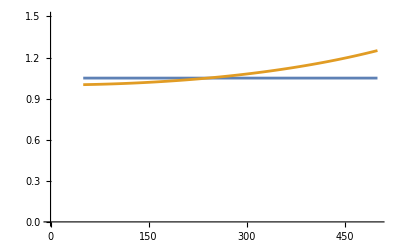

```mathematica
Plot[{1.05,1/Abs[ Cosh[γ x]]},{x, 50, 500}, PlotRange->{0, 1.5}]
```

## Circuito simples de 500 kV (500CSH1)

para o condutor Rail

```mathematica
Vn= 500.;
z1 = 0.0175+I .3179;
y1= I 10^-6 5.1896;
```

```mathematica
Zc= Sqrt[z1/y1]
```

247.595-6.80976 ⅈ

```mathematica
Pn = Vn^2/Zc
```

1008.95+27.7497 ⅈ

```mathematica
γ= Sqrt[z1 y1];
```

```mathematica
ℓ= 250.;
```

```mathematica
a=Cosh[γ ℓ];
b= Zc Sinh[γ ℓ];
c= 1/Zc Sinh[γ ℓ];
```

```mathematica
Q={{a,b},{c,a}};
MatrixForm[Q]
```

(0.948885+0.00278954 ⅈ | 4.22579+78.1203 ⅈ
-1.21476×10^-6+0.00127522 ⅈ | 0.948885+0.00278954 ⅈ)

```mathematica
Abs[1/a]
```

1.05386

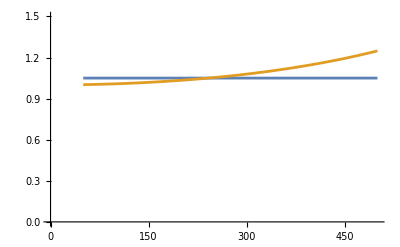

```mathematica
Plot[{1.05,1/Abs[ Cosh[γ x]]},{x, 50, 500}, PlotRange->{0, 1.5}]
```

```mathematica
vr= 500. 10^3/ Sqrt[3];
ir =vr/Re[Zc]
```

1165.91

```mathematica
{vs, is} = Q.{vr, ir};
```

```mathematica
sin=3vs Conjugate[is]
```

1.02756×10^9-5.79885×10^6 ⅈ

```mathematica
Re[Pn] 10^6
```

1.00895×10^9

```mathematica
perdas=(Re[sin]-10^6 Re[Pn])/10^6
```

18.6106

```mathematica
100 perdas/Re[Pn]
```

1.84455